```mathematica
L = 20;  (* number of lattice points on a side (assume symmetric volume) *)
(* Please choose an even L for now!!! *)
```

```mathematica
(* 
Ok,this routine tabulates all triplet of integers 
nx^2+ny^2+nz^2 
such that each component satisfies 
-L/2 < Subscript[n, i] ≤ L/2 .  
The Table[] routine will have degenerate values of 
N^2= nx^2+ny^2+nz^2, 
and so the Tally[] routine will actually determine the degeneracy of each N^2.  The table is outputted as {N^2, degeneracy}.  The Sort[] function just orders the list in terms of ascending values of N^2. 
*)
gn=Sort[Tally[Flatten[Table[nx^2+ny^2+nz^2,{nx,-L/2+1,L/2},{ny,-L/2+1,L/2},{nz,-L/2+1,L/2}]]]];
```

```mathematica
(* Now this is the numerical coefficient to the counter term, evaluated from
Λ=1;
4π 8/((2 π)^3 Λ)NIntegrate[1/(x^2+y^2+z^2),{x,0,Λ},{y,0,Λ},{z,0,Λ},WorkingPrecision->18]
Note that the value is independent of Λ!!!
*)
Lb=0.77755134969592873086316106575075368089`18.;
```

```mathematica
(* Now here is the routine that calculates the "cartesian S-function" *)
S[x_]:=Module[{S3},
S3=Sum[gn[[i,2]]/(gn[[i,1]]-x),{i,1,Length[gn]}];
Return[S3- 2 π^2 Lb (L/2)];
];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

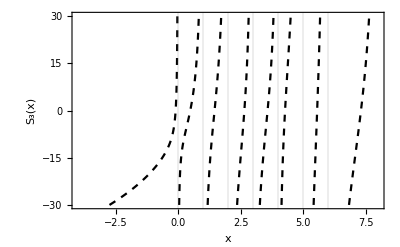

```mathematica
(* Let's plot this function out *)
S3cart=ListPlot[Table[{x,S[x]},{x,-4.0,8.0,.001}],PlotRange->{{-4,8},{-30,30}},Frame->True,FrameStyle->Directive[Black,14],GridLines->{{0,1,2,3,4,5,6},None},FrameLabel->{"x","S_3(x)"},Joined->True,PlotStyle->{Black,Dashed}]
```

```mathematica
(* Let's determine the zero of S3[x] for x < 0.  This is what Christopher would have to retune his bound state to. *)
FindRoot[S[x],{x,-0.09}]
```

{x→-0.0953057}

```mathematica
(* Here are the zeros for the scattering states *)
FindRoot[S[x],{x,.48}]
FindRoot[S[x],{x,1.5}]
FindRoot[S[x],{x,2.6}]
FindRoot[S[x],{x,3.6}]
FindRoot[S[x],{x,4.3}]
FindRoot[S[x],{x,5.5}]
```

{x→0.489909}

{x→1.46231}

{x→2.65412}

{x→3.58295}

{x→4.28237}

{x→5.5659}

```mathematica
(* For the hell of it, let me just plug in the values of x that Christopher found from his numerical calculation, bearing in mind that his tuning for the bound state was NOT correct (since it was done using a spherical, cotinuum S3) *)
S[-0.09612412]
S[0.4879434]
S[1.46175079]
S[2.65395876]
S[3.58273158]
S[4.28221617]
S[5.56572774]
```

-0.100827

-0.0785074

-0.0460086

-0.0175565

-0.0189375

-0.0220635

-0.0386007

```mathematica
(* Compare this to the results using the continuum S3 function (in spherical coordinates) NB: to evaulate these numbers, I used my original Mma notebook that defines the function Z[] *)
2 Sqrt[π]Z[-0.09612412]
2 Sqrt[π] Z[0.4879434]
2 Sqrt[π] Z[1.46175079]
2 Sqrt[π] Z[2.65395876]
2 Sqrt[π] Z[3.58273158]
2 Sqrt[π] Z[4.28221617]
2 Sqrt[π] Z[5.56572774]
```

-0.0276795

0.606739

1.66366

2.95299

3.93906

4.68264

6.04315

```mathematica
(* Even though the tuning of the bound state was incorrect, the scattering states are all much closer to zero when one uses the cartesian S-function!!!  I think this means once Christopher re-tunes his bound state, the slope will essentially go to zero! *)
```

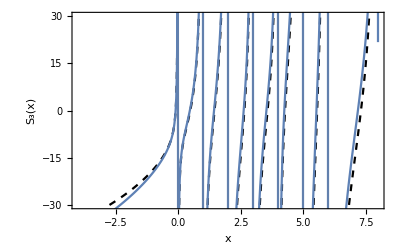

```mathematica
Show[S3cart,ListPlot[Table[{zdat[[i,1]],2 Sqrt[π]zdat[[i,2]]},{i,1,Length[zdat]}],Joined->True]]
```